#### 1)

```mathematica
f=1/x^2+√x;
g=ArcSin[x]/Log[x];
h=x^4 Sin[x^2];
D[f,x]
D[g,x]
D[h,x]
```

-2/x^3+1/(2 √x)

-ArcSin[x]/(x Log[x]^2)+1/(√(1-x^2) Log[x])

2 x^5 Cos[x^2]+4 x^3 Sin[x^2]

#### 2)

```mathematica
f=x^(1/2);
Series[f,{x,1,2}]//Normal
%/.{x->1.1}
Sqrt[1.1]
```

1+1/2 (-1+x)-1/8 (-1+x)^2

1.04875

1.04881

#### 3)

-6 x-3 x^2+8 x^3+6 x^4

-6-6 x+24 x^2+24 x^3

{{x→-1},{x→-1/2},{x→1/2}}

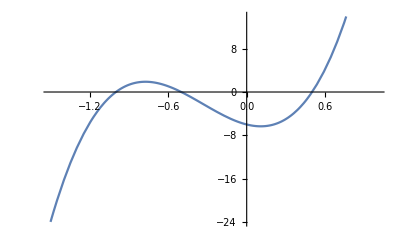

6 x^4+8 x^3-3 x^2-6 x

```mathematica
(x+1)(4 x^2-1)//Expand;
y1=Integrate[%,x]6//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-1.5,1}]
y1//TeXForm
```

#### 4)

```mathematica
Apart[(3x+1)/(x^2-4x+3)]
Integrate[%,x]
```

5/(-3+x)-2/(-1+x)

-2 Log[1-x]+5 Log[3-x]

#### 5)

```mathematica
Integrate[3 x^2+2/x^2,{x,1,2}]
Integrate[x^2 (1+x^3)^3,{x,-1,1}]
```

8

4/3

#### 6)

{{x→-1},{x→1}}

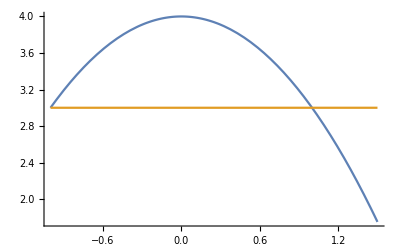

4/3

```mathematica
y1=4-x^2;
y2=3;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1,1.5}]
Integrate[y1-y2,{x,-1,1}]
```